# Verdampfungswäre

## 1. Bestimmung des Wasserwertes W vom Dewar - Gefäß

1. Auffüllen des Dewar-Gefäßes mit klaten Wasser T_k

2.  Nach ein paar Minuten wieder ausleeren

```mathematica
mBecher = 673 10^-3(*kg*);
dmBecher=2*10^-3(*kg*);(*Balkenwaage*)
mGesamt =1098 10^-3(*kg*);
dmGesamt=2*10^-3(*kg*);(*Balkenwaage*)
mWasserWarm = mGesamt - mBecher//N
dmWasserWarm = dmGesamt+dmBecher//N
```

0.425

0.004

3.  Warmes Wasser 3 min messen (T/°C, t/s)

```mathematica
dataW = {{"t/s", 0, 30, 60, 90, 120, 150, 180}, {"T/°C", 48.8, 48.1, 47.8, 47.2, 47.0, 46.6, 46.5}}(*für Warmes Wasser*);
ddataW = {{2}, {0.2}}(*Fehler*);
```

4.Einschütten von warmen Wasser T_w, m_w

```mathematica
tm= 3*60+35
dtm=4
```

215

4

```mathematica
dataM = {{"t/s", 240, 270, 300, 330, 360, 390, 420}, {"T/°C", 43.6, 43.6, 43.6, 43.6, 43.6, 43.6, 43.6}}(*für Gemischtes Wasser*);
ddataW = {{2}, {0.2}}(*Fehler*);
```

5. Differenztemperatur zurückrechnen

```mathematica
Table[{dataW[[1,i]],dataW[[2,i]]},{i,2,Dimensions[dataW][[2]]}];
```

```mathematica
fitWdata=Table[{dataW[[1,i]],dataW[[2,i]]},{i,2,Dimensions[dataW][[2]]}];
fitW = LinearModelFit[fitWdata,x,x]
```

FittedModel[48.575-0.0127381 x]

```mathematica
0.0127281*100
```

1.27281

```mathematica
fitMdata=Table[{dataM[[1,i]],dataM[[2,i]]},{i,2,Dimensions[dataM][[2]]}];
fitM = LinearModelFit[fitMdata,x,x]
```

FittedModel[43.6-2.00173×10^-16 x]

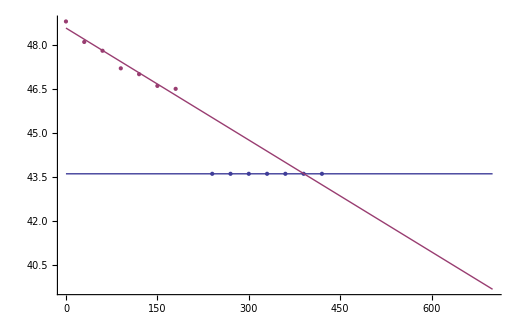

```mathematica
Show[ListPlot[{fitMdata,fitWdata}],Plot[{fitM[i],fitW[i]},{i,0,700}]]
```

```mathematica
Tm=fitM[tm]
dTm = 7*0.05;
Tw = fitW[tm]
dTw=7*0.05;
Tk=0;
dTk=0.2;
```

43.6

45.8363

```mathematica
c0=1000(*cal*);b
dc0=0;
```

```mathematica
GError[a_,b_,c_]:= (Total[Map[Abs,MapThread[D,{Table[a,{i,1,Length[b]}],b}]]*c]);
W[mw_,co_,Tw_,Tm_,Tk_,dmw_,dco_,dTm_,dTw_,dTk_]:=Module[{vmw,vco,vTm,vTw,vTk,vdmw,vdco,vdTm,vdTw,vdTk,f,fe},
f=(vmw vco (vTw-vTm))/(vTm-vTk);
fe=GError[f,{vmw,vco,vTm,vTw,vTk},{vdmw,vdco,vdTm,vdTw,vdTk}];
{f,fe}/.{vmw->mw,vco->co,vTm->Tm,vTw->Tw,vTk->Tk,vdmw->dmw,vdco->dco,vdTm->dTm,vdTw->dTw,vdTk->dTk}]
```

```mathematica
WW=W[mWasserWarm,c0,Tw,Tm,Tk,dmWasserWarm,dc0,dTm,dTw,dTk]
```

{21.7989,7.30355}

## 2. Bestimmung der Verdampfungswärme von Wasser

Wiegen der leeren Thermosflasche

```mathematica
m0=mBecher(*kg*)//N
dm0=dmBecher(*kg*)//N
```

0.673

0.002

Füllen mit klatem Wasser

```mathematica
mMitWasser=990 10^-3(*kg*);
dmMitWasser = 2 10^-3(*kg*);
m1 = mMitWasser -m0//N
dm1 = dm0 + dmMitWasser//N
```

0.317

0.004

Wasserdampf einleiten bis ~50 °C, vorher schon T messen , Zwickelabgleich für T1 T2

```mathematica
T1 = 23.2(*°C*)
dT1 = 1
T2 = 72.5
dT2 = 1
```

23.2

1

72.5

1

Wiegen mit warmem Wasser

```mathematica
mMitWarmemWasser = 1020 10^-3
dmMitWarmemWasser = 2 10^-3
m2 = mMitWarmemWasser - mMitWasser//N
dm2 = dmMitWarmemWasser + dmMitWasser//N
```

51/50

1/500

0.03

0.004

```mathematica
r[vm1_,vco_,vW_,vT2_,vT1_,vm2_,vdm1_,vdco_,vdW_,vdT2_,vdT1_,vdm2_]:=Module[{f,fe,fr,m1,c0,W,T2,T1,m2,dm1,dc0,dW,dT2,dT1,dm2},
f=((m1 c0 + W)(T2-T1))/m2-(100-T2)c0;
fe=GError[f,{m1,c0,W,T2,T1,m2},{dm1,dc0,dW,dT2,dT1,dm2}];
fr = ((dm1 c0 +dW)/(c0 +W)+dT1/(T2-T1)+dT2/(T2-T1)+dm2/m2)(f+c0(100-T2))+c0 dT2;
{f,fe,fr}/.{m1->vm1,c0->vco,W->vW,T2->vT2,T1->vT1,m2->vm2,dm1->vdm1,dc0->vdco,dW->vdW,dT2->vdT2,dT1->vdT1,dm2->vdm2}]
```

```mathematica
{m1,c0,WW[[1]],T2,T1,m2,dm1,dc0,WW[[2]],dT2,dT1,dm2}
```

{0.317,1000,21.7989,72.5,23.2,0.02,0.004,0,7.30355,1,1,0.004}

```mathematica
r[m1,c0,WW[[1]],T2,T1,m2,dm1,dc0,WW[[2]],dT2,dT1,dm2]
```

{529260.,116397.,103980.}

```mathematica
{739997.4743337695,197489.3181435029,180317.45866218742}
```

{739997.,197489.,180317.}